# Electric Field by parallel plate Capacitor

```mathematica
G[x_,y_,z_,xx_,yy_,zz_]:=1/(√((x-xx)^2+(y-yy)^2+(z-zz)^2))-1/(√((x+xx)^2+(y+yy)^2+(z+zz)^2))
```

```mathematica
D[G[x,y,z,xx,yy,zz],zz]/.zz->d
```

(-d+z)/(((x-xx)^2+(y-yy)^2+(-d+z)^2)^(3/2))+(d+z)/(((x+xx)^2+(y+yy)^2+(d+z)^2)^(3/2))

```mathematica
Φ[x_,y_,z_,W_,L_,d_]:=(ArcTan[((L-y)(W-x))/((z-d)√((z-d)^2+(W-x)^2+(L-y)^2))]+ArcTan[((L+y)(W-x))/((z-d)√((z-d)^2+(W-x)^2+(L+y)^2))]+ArcTan[((L-y)(W+x))/((z-d)√((z-d)^2+(W+x)^2+(L-y)^2)) ]+ArcTan[((L+y)(W+x))/((z-d)√((z-d)^2+(W+x)^2+(L+y)^2))])
```

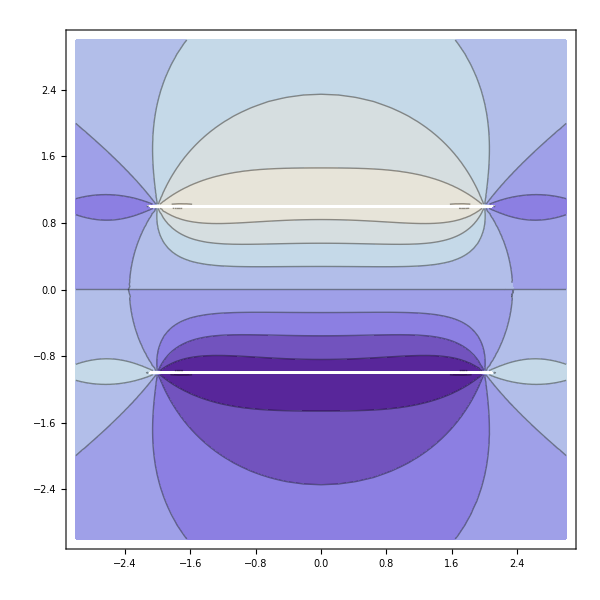

```mathematica
ContourPlot[
Abs[Φ[0,y,z,4,2,1]]-Abs[Φ[0,y,z,4,2,-1]]
,{y,-3,3},{z,-3,3},Exclusions->{{z==1,Abs[y]<2.1},{z==-1,Abs[y]<2.1}},ImageSize->600]
```

```mathematica
Manipulate[
Plot[{Abs[Φ[0,y,z,10,20,1]],
-Abs[Φ[0,y,z,10,20,-1]],
Abs[Φ[0,y,z,10,20,1]]-Abs[Φ[0,y,z,10,20,-1]]
}
,{z,-3,3},ImageSize->600],
{y,0,30}
]
```

```mathematica
Needs["VectorAnalysis`"]
Grad[Abs[Φ[x,y,z,W,L,d]],Cartesian[x,y,z]]//Simplify
```

$Aborted

```mathematica
Ex[x_,y_,z_,W_,L_,d_]:=(z-d) ((L-y)/(((W+x)^2+(z-d)^2) √((W+x)^2+(L-y)^2+(z-d)^2))-(L-y)/(((W-x)^2+(z-d)^2) √((L-y)^2+(W-x)^2+(z-d)^2))-(L+y)/(((W-x)^2+(z-d)^2) √((W-x)^2+(L+y)^2+(z-d)^2))+(L+y)/(((W+x)^2+(z-d)^2) √((W+x)^2+(L+y)^2+(z-d)^2)))
Ey[x_,y_,z_,W_,L_,d_]:=(z-d) ((W-x)/(((L+y)^2+(z-d)^2) √((W-x)^2+(L+y)^2+(z-d)^2))-(W-x)/(((L-y)^2+(z-d)^2) √((L-y)^2+(W-x)^2+(z-d)^2))-(W+x)/(((L-y)^2+(z-d)^2)√((W+x)^2+(L-y)^2+(z-d)^2))+(W+x)/(((L+y)^2+(z-d)^2) √((W+x)^2+(L+y)^2+(z-d)^2)))
Ez[x_,y_,z_,W_,L_,d_]:=-((W-x) (L-y) ((L-y)^2+(W-x)^2+2 (z-d)^2))/(((W-x)^2+(z-d)^2) ((L-y)^2+(z-d)^2) √((W-x)^2+(L-y)^2+(z-d)^2))-((W+x) (L-y) ((L-y)^2+(W+x)^2+2 (z-d)^2))/(((W+x)^2+(z-d)^2) ((L-y)^2+(z-d)^2)√((W+x)^2+(L-y)^2+(z-d)^2))-((W-x) (L+y) ((L+y)^2+(W-x)^2+2 (z-d)^2))/(((W-x)^2+(z-d)^2) ((L+y)^2+(z-d)^2) √((W-x)^2+(L+y)^2+(z-d)^2))-((W+x) (L+y) ((L+y)^2+(W+x)^2+2 (z-d)^2))/(((W+x)^2+(z-d)^2) ((L+y)^2+(z-d)^2) √((W+x)^2+(L+y)^2+(z-d)^2))
```

```mathematica
Manipulate[
StreamDensityPlot[
Piecewise[{
{{-Ey[0,y,z,W,L,d],-Ez[0,y,z,W,L,d]},z>d},
{{Ey[0,y,z,W,L,d],Ez[0,y,z,W,L,d]},z<d}
}]
+Piecewise[{
{{Ey[0,y,z,W,L,-d],Ez[0,y,z,W,L,-d]},z>-d},
{-{Ey[0,y,z,W,L,-d],Ez[0,y,z,W,L,-d]},z<-d}
}]
,{y,-5,5},{z,-5,5},
StreamPoints->Fine, StreamColorFunction->"Rainbow",ColorFunction->Hue,
AspectRatio->1,ImageSize->700]
,
{{W,1},0,5},
{{L,2},0,5},
{{d,1},0,5}]
```